## 5강 미분과 적분

전경원 <ruddyscent@gmail.com>

2014년 10월 27일 화요일

```mathematica
$Version
DateString[]
```

10.0 for Microsoft Windows (32-bit) (September 9, 2014)

Tue 11 Nov 2014 11:39:35

## 극한

다음과 같은 함수를 분석해봅시다.

```mathematica
Clear[f,g,x];
f[x_]:=Sin[x]/x
g[x_]:=1/x
```

함수를 분석할 때 처음 해볼 일은 무엇보다 그래프 그리기죠.

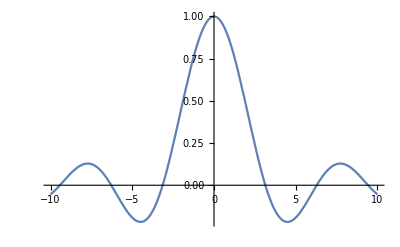

```mathematica
Plot[f[x],{x,-10,10}]
```

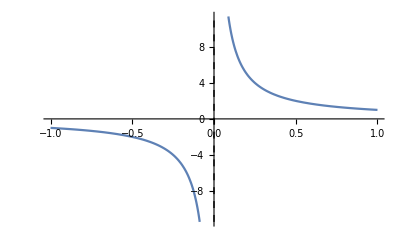

```mathematica
Plot[g[x],{x,-1,1},Exclusions->x==0,ExclusionsStyle->{Dashed}]
```

x=0 근처에서 함수의 값을 관찰해 볼까요?

```mathematica
data=Table[{N[10^-n],N[f[10^-n],15]},{n,1,5}];
Text@Grid[Prepend[data,{"x","f(x)"}],Alignment->Left,Dividers->{Center,2->True}]
```

x | f(x)
0.1 | 0.998334166468282
0.01 | 0.999983333416666
0.001 | 0.999999833333342
0.0001 | 0.999999998333333
0.00001 | 0.999999999983333

Limit 명령을 이용하면 이러한 경향을 간단하게 파악할 수 있습니다.

```mathematica
Limit[f[x],x->0]
```

1

```mathematica
Limit[g[x],x->0]
```

∞

매스매티카의 극한은 기본적으로 우극한입니다. 좌극한을 구하고자 한다면,

```mathematica
Limit[g[x],x->0,Direction->1]
```

-∞

수학적 정의로는 좌우극한이 일치하는 경우에만 극한이 존재하는 것이므로, 반드시 좌우 극한을 확인해야 합니다.

한쪽 극한조차 없는 경우도 있습니다.

```mathematica
Limit[Sin[x],x->∞]
```

Interval[{-1,1}]

```mathematica
Limit[Sin[1/x],x->0]
```

그래프를 그려보면 명확하지요.

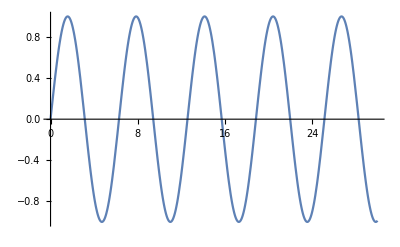

```mathematica
Plot[Sin[x],{x,0,30}]
```

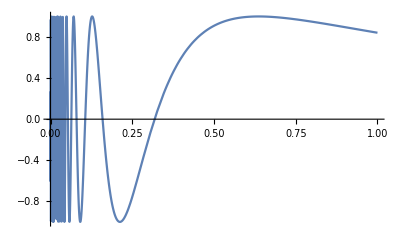

```mathematica
Plot[Sin[1/x],{x,0,1}]
```

Piecewise 명령으로 정의된 함수는 좌우 극한이 다른 전형적인 예입니다.

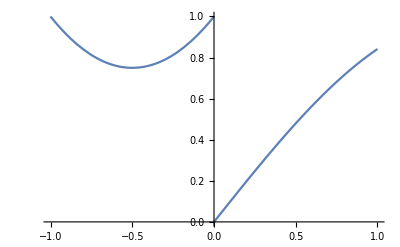

```mathematica
Plot[Piecewise[{{x^2+x+1, x≤0}, {Sin[x], x>0}}],{x,-1,1}]
```

```mathematica
Limit[Piecewise[{{x^2+x+1, x≤0}, {Sin[x], x>0}}],x->0,Direction->1]
```

1

```mathematica
Limit[Piecewise[{{x^2+x+1, x≤0}, {Sin[x], x>0}}],x->0,Direction->-1]
```

0

수식이 극한값에 영향을 미치는 변수를 또 하나 포함하고 있을 수도 있지요.

```mathematica
Clear[x,n];
Limit[(1-x^n)/n,x->0]
```

Limit[(1-x^n)/n,x→0]

이 식에서는 극한 값을 결정하려면, n에 대한 정보가 필요합니다.

```mathematica
Clear[x,n];
Assuming[n>0,Limit[(1-x^n)/n,x->0]]
```

1/n

```mathematica
Clear[x,n];
Limit[(1-x^n)/n,x->0,Assumptions->n<0]
```

∞

## 평균 변화율(Difference Quotients)

함수의 평균 변화율은 아래와 같이 정의 됩니다.

```mathematica
Clear[diffquot,x,Δx]
diffquot[f_]:=(f[x+Δx]-f[x])/Δx
```

x=2에서 x=2.5까지 f(x)=(sin(π x))/x의 함수 변화율을 알아볼까요?

```mathematica
Clear[f,x,Δx]
f[x_]:=Sin[π x]/x
```

```mathematica
diffquot[f]
%/.{ x->2,Δx->0.5}
```

(-Sin[π x]/x+Sin[π (x+Δx)]/(x+Δx))/Δx

0.8

Δx를 줄여 나가 볼까요?

```mathematica
data=Table[{Δx,diffquot[f]}/.{x->2,Δx->N[10^-n]},{n,1,5}];
dataWithHeadings=Prepend[data,{"Δx","(f (2 + ΔX) - f (2))/Δx"}];
Text@Grid[dataWithHeadings,Alignment->Left,Dividers->{Center,2->True}]
```

Δx | (f (2 + ΔX) - f (2))/Δx
0.1 | 1.47151
0.01 | 1.56272
0.001 | 1.57001
0.0001 | 1.57072
0.00001 | 1.57079

Δx가 0으로 접근할 때의 편균 변화율 값을 순간 변화율이라고 합니다.

```mathematica
diffquot[f]/.x->2
Limit[%,Δx->0]
N[%,10]
```

## 미분

미분을 구하는데, 이렇게 어렵게 하지 않아도 됩니다.

```mathematica
f'[x]
%//Simplify
```

(π Cos[π x])/x-Sin[π x]/x^2

(π x Cos[π x]-Sin[π x])/x^2

특정 x에서 미분값을 구하려면,

```mathematica
f'[2]
```

π/2

함수와 특정 x에서의 접선은 아래와 같이 그릴 수 있습니다.

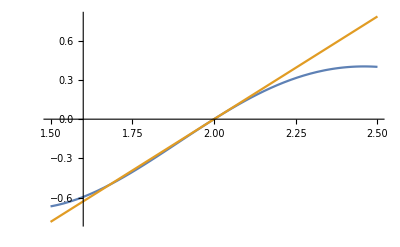

```mathematica
Plot[{f[x],f[2]+f'[2]*(x-2)},{x,1.5,2.5}]
```

함수와 그 미분값을 같이 그려볼까요?

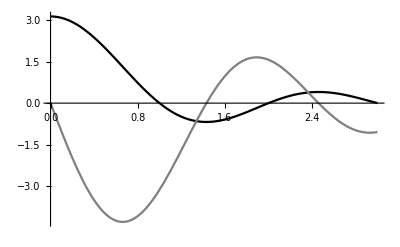

```mathematica
Plot[{f[x],f'[x]},{x,0,3},PlotStyle->{Black,Gray}]
```

이렇게 미분할 수도 있습니다.

```mathematica
D[Sin[π x]/x,x]
```

(π Cos[π x])/x-Sin[π x]/x^2

이렇게도 할 수 있고요.

```mathematica
D[Sin[x], x]
```

Cos[x]

D 명령어가 들어간 표현을 그래프로 그리고자 한다면, Evaluate 명령으로 한번 감싸주세요.

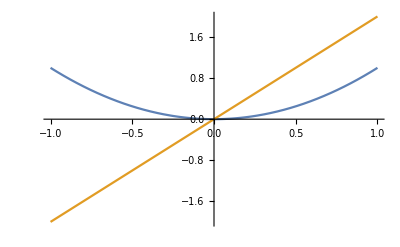

```mathematica
Plot[Evaluate@{x^2,D[x^2,x]},{x,-1,1}]
```

## 미분의 시각적 접근

sin(x)의 미분이 cos(x)인 걸 시각적으로 확인할 수 있죠.

```mathematica
Manipulate[Plot[{(Sin[x+Δx]-Sin[x])/Δx,Cos[x]},{x,-2π,2π}],{Δx,2,.01}]
```

## 고차미분

```mathematica
Clear[f,x]
f[x_]:=Sin[π x]/x
```

이차미분은 간단하게,

```mathematica
f''[x]
```

-(2 π Cos[π x])/x^2+(2 Sin[π x])/x^3-(π^2 Sin[π x])/x

삼차미분은?

```mathematica
f'''[x]
```

(6 π Cos[π x])/x^3-(π^3 Cos[π x])/x-(6 Sin[π x])/x^4+(3 π^2 Sin[π x])/x^2

다른 방법으로는

```mathematica
D[f[x],{x,3}]
```

(6 π Cos[π x])/x^3-(π^3 Cos[π x])/x-(6 Sin[π x])/x^4+(3 π^2 Sin[π x])/x^2

## 최댓값과 최솟값

함수 f의 미분값이 0인 x를 찾으려면

```mathematica
Clear[f,x];
f[x_]:=x^3-9x+5
```

```mathematica
Reduce[f'[x]==0,x]
```

x==-√3||x==√3

```mathematica
Solve[f'[x]==0,x]
```

{{x→-√3},{x→√3}}

이 x 값의 함수값이 f의 극한이 되겠죠.

```mathematica
extrema={x,f[x]}/.%
```

{{-√3,5+6 √3},{√3,5-6 √3}}

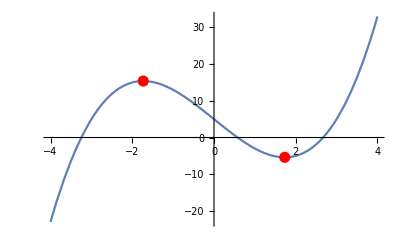

```mathematica
Plot[f[x],{x,-4,4},Epilog->{PointSize[0.02],Red,Point[extrema]}]
```

이차미분을 구해보면, 이 극한값이 최솟값인지 최댓값인지 알 수 있습니다.

```mathematica
{f''[-√3],f''[√3]}
```

{-6 √3,6 √3}

Solve나 NSolve 명령이 f'(x)=0을 풀 수 없다면, 어떻게 하죠?

```mathematica
f[x_]:=Sin[π x]/x
```

```mathematica
Reduce[f'[x]==0,x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(π Cos[π x])/x-Sin[π x]/x^2==0,x]

```mathematica
NSolve[f'[x]==0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[(π Cos[π x])/x-Sin[π x]/x^2==0,x]

첫 걸음은 역시 그래프 그리기.

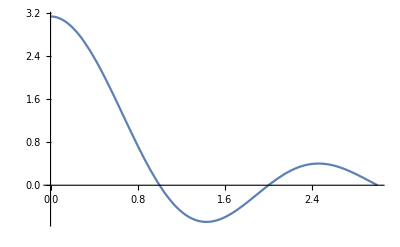

```mathematica
Plot[f[x],{x,0,3}]
```

x=1.5 근처에서 최솟값이 있군요.

```mathematica
FindRoot[f'[x]==0,{x,1.5}]
minpoint={x,f[x]}/.%
```

{x→1.4303}

{1.4303,-0.68246}

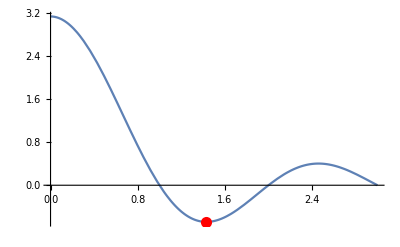

```mathematica
Plot[f[x],{x,0,3},Epilog->{PointSize[0.02],Red,Point[minpoint]}]
```

f'(x)=0을 만족한다고 해서, 꼭 극한 값인 것은 아닙니다.

```mathematica
f[x_]:=8.01+12x-6 x^2+x^3
```

```mathematica
NSolve[f'[x]==0,x]
```

{{x→2.},{x→2.}}

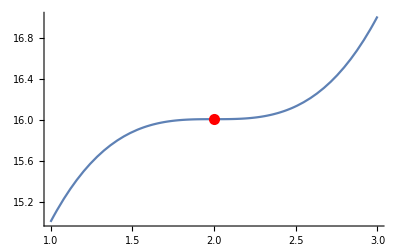

```mathematica
Plot[f[x],{x,1,3},Epilog->{PointSize[0.02],Red,Point[{2,f[2]}]}]
```

이차미분을 구해보면 더욱 확연하죠.

```mathematica
f''[2]
```

0

다음 예에선 Solve는 극한을 찾지 못하지만, Reduce는 모든 극한을 다 찾아냅니다.

```mathematica
f[x_]:=Cos[π ⅇ^x]
```

```mathematica
f'[x]
```

-ⅇ^x π Sin[ⅇ^x π]

```mathematica
Solve[f'[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-∞}}

```mathematica
Reduce[f'[x]==0,x,Reals]//Simplify
```

C[1]∈Integers&&((C[1]≥1&&x==Log[2 C[1]])||(C[1]≥0&&x==Log[1+2 C[1]]))

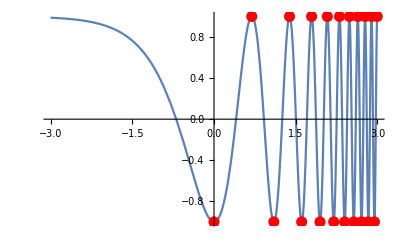

```mathematica
Plot[f[x],{x,-3,3},Epilog->{PointSize[0.02],Red,Point[Table[{Log[c],f[Log[c]]},{c,20}]]}]
```

매스매티카엔 이런 과정을 간편하게 해줄 명령이 있습니다.

```mathematica
Clear[f,x]
f[x_]:=x^3-9x+5;
Maximize[f[x],x]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{x→∞}}

제약 조건을 줘 볼까요?

```mathematica
Maximize[{f[x],-4≤x≤0},x]
```

{5+6 √3,{x→-√3}}

이 구간에서 최솟값은 왼쪽 경계에 있군요.

```mathematica
Minimize[{f[x],-4≤x≤0},x]
```

{-23,{x→-4}}

그럼, 문제를 풀어봅시다. 반듯이 흐르는 냇가로 맊힌 초원에 직사각형의 울타리를 두른다고 합니다. 1km의 울타리가 준비뒤어 있다면, 이 울타리로 두를 수 있는 최대 면적은 얼마일까요?

```mathematica
Maximize[{x y,2x+y==1000},{x,y}]
```

{125000,{x→250,y→500}}

```mathematica
Manipulate[
Module[{y},
y:=1000-2x;
GraphicsRow[{
Plot[y,{x,0,500},AspectRatio->.5,
Epilog->{Gray,EdgeForm[Black],Polygon[{{0,0},{x,0},{x,y},{0,y}}]},
AxesLabel->{"x","y"},Ticks->{{0,250,500},Automatic}],
Plot[x y,{x,0,500},AspectRatio->.5,
Epilog->{PointSize[.04],Red,Point[{x,x y}]},
AxesLabel->{"x","Area of Rectangle"}]},ImageSize->600]],
{{x,250},0,500}]
```

## 변곡점

```mathematica
Clear[f,x]
f[x_]:=Sin[π x]/x
```

f'이 음수이면 f는 감소하고, f'이 양수이면 f는 증가합니다. f'이 0이라면 f의 극한값이 존재할 수 있습니다.

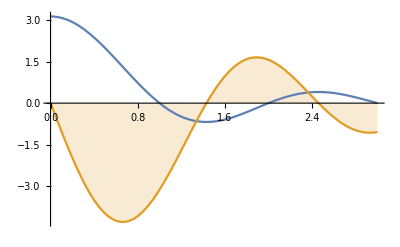

```mathematica
Plot[{f[x],f'[x]},{x,0,3},Filling->{2->Axis}]
```

f''가 음수라면 f는 위로 볼록하게 되고, f''가 양수라면 아래로 볼록하게 됩니다. f''가 0이라면 변곡점이 됩니다.

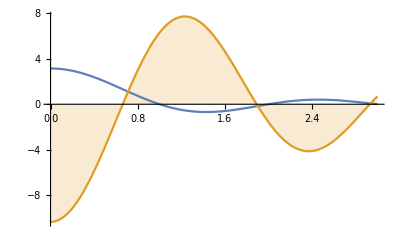

```mathematica
Plot[{f[x],f''[x]},{x,0,3},Filling->{2->Axis}]
```

## 음함수의 미분

cos(x^2)-sin(y^2)=0의 ⅆy/ⅆx를 구해봅시다.

Here’s how to find ⅆy/ⅆx for the implicit equation cos(x^2)-sin(y^2)=0.

```mathematica
Clear[x,y]
lhs=D[Cos[x^2]-Sin[y[x]^2],x]
```

-2 x Sin[x^2]-2 Cos[y[x]^2] y[x] y'[x]

우변은 0이니까,

```mathematica
Solve[lhs==0,y'[x]]
```

{{y'[x]→-(x Sec[y[x]^2] Sin[x^2])/y[x]}}

x와 y가 또 다른 변수 t와 관련되어 있을 수도 있습니다.

```mathematica
Clear[x,y,t]
lhs=D[Cos[x[t]^2]-Sin[y[t]^2],t]
```

-2 Sin[x[t]^2] x[t] x'[t]-2 Cos[y[t]^2] y[t] y'[t]

```mathematica
Solve[lhs==0,x'[t]]
```

{{x'[t]→-(Cos[y[t]^2] Csc[x[t]^2] y[t] y'[t])/x[t]}}

```mathematica
Solve[lhs==0,y'[t]]
```

{{y'[t]→-(Sec[y[t]^2] Sin[x[t]^2] x[t] x'[t])/y[t]}}

## 미분방정식

어느 시점 t에서의 인구를 y(t)라고 하면, 인구 증가율 y'(t)는 현재의 인구 y(t)의 1/3에 해당한다고 해보자.

```mathematica
Clear[y,t]
DSolve[y'[t]==1/3 y[t],y[t],t]
```

{{y[t]→ⅇ^(t/3) C[1]}}

초기 인구를 400명이라고 한다면,

```mathematica
y[t]/.%[[1]]/.C[1]->400
```

400 ⅇ^(t/3)

이러한 조건을 DSolve의 첫 번째 인자로 줄 수 있습니다.

{{y[t]→400 ⅇ^(t/3)}}

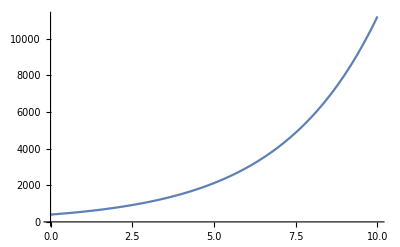

```mathematica
Clear[y,t]
DSolve[{y'[t]==1/3 y[t],y[0]==400},y[t],t]
Plot[y[t]/.%,{t,0,10}]
```

NSolve가 Solve를 보조해주는 것처럼, DSolve가 역할을 못할 때엔 NDSolve가 그 자릴 대신합니다.

{{y[t]→InterpolatingFunction[{{0., 200.}}, <>][t]}}

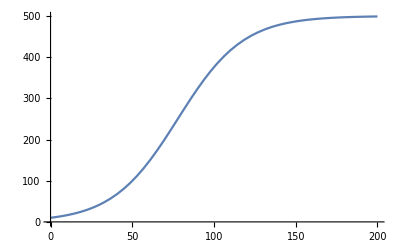

```mathematica
sols=NDSolve[{y'[t]==0.05y[t]-0.0001 y[t]^2,y[0]==10},y[t],{t,0,200}]
Plot[y[t]/.sols,{t,0,200}]
```

## 적분

```mathematica
∫1/(1-x^3)ⅆx
```

ArcTan[(1+2 x)/(√3)]/(√3)-1/3 Log[1-x]+1/6 Log[1+x+x^2]

Integrate 명령어를 직접 쓸 수도 있죠.

```mathematica
Integrate[ArcTan[x],x]
```

x ArcTan[x]-1/2 Log[1+x^2]

매스매티카는 가장 간단한 결과를 출력한다는 점을 명심해야 합니다.

적분 공식을 얻는데, 활용할 수도 있습니다.

```mathematica
Clear[n,x]
∫x^n ⅆx
```

x^(1+n)/(1+n)

이 공식은 n≠-1일 때만 성립한다는 점은 사용자가 파악해야 합니다.

체인룰도 확인할 수 있습니다.

```mathematica
Clear[F,u,x];
∫F'[u[x]]u'[x]ⅆx
```

F[u[x]]

변수를 실수로만 제한하고 싶다면,

```mathematica
Assuming[t∈Reals,∫√(t^4+2 t^2+1)ⅆt]
```

t+t^3/3

Integrate 명령 안에서 해결할 수도 있죠.

```mathematica
Integrate[√(t^4+2 t^2+1),t,Assumptions->t∈Reals]
```

t+t^3/3

## 정적분

```mathematica
∫_-2^2 (1-x^2)ⅆx
```

-4/3

```mathematica
Integrate[1-x^2,{x,-2,2}]
```

-4/3

적분한 값은 x 축 위로의 영역에서 x 축 아래의 영역을 뺀 값입니다.

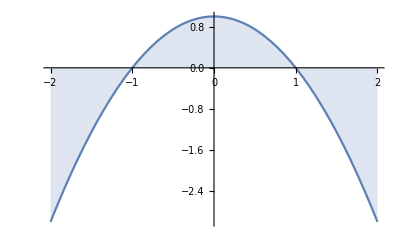

```mathematica
Plot[1-x^2,{x,-2,2},Filling->Axis]
```

## 수치적분

NIntegrate 명령은 수치 적분을 효율적으로 계산해냅니다. Integrate 명령이 계산하지 못하는 적분까지도요.

```mathematica
Integrate[√ArcTan[t],{t,0,1}]
```

∫_0^1 √ArcTan[t]ⅆt

```mathematica
NIntegrate[√ArcTan[t],{t,0,1}]
```

0.629823

```mathematica
∫_0^1 √(t^4+2 t^2+2)ⅆt
%//N
%//Chop
```

1/3 (√5-2 √(-1+ⅈ) EllipticE[ⅈ ArcSinh[√(1/2-ⅈ/2)],ⅈ]+2 √(1-ⅈ) EllipticF[ⅈ ArcSinh[√(1/2-ⅈ/2)],ⅈ])

1.67571+7.40149×10^-17 ⅈ

1.67571

```mathematica
NIntegrate[√(t^4+2 t^2+2),{t,0,1}]
```

1.67571

정의역을 너무 넒게 잡으면 Plot 명령이 함수의 세부 모습을 놓치는 것처럼, NIntegrate 명령도 함수의 세부 모습을 놓치기도 합니다.

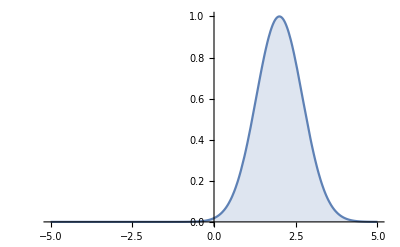

```mathematica
Plot[ⅇ^(-(x-2)^2),{x,-5,5},PlotRange->{0,1},Filling->Axis]
```

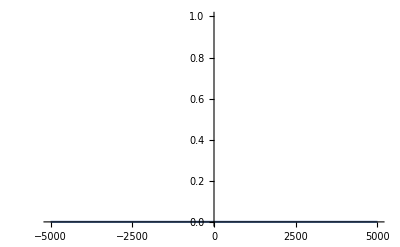

```mathematica
Plot[ⅇ^(-(x-2)^2),{x,-5000,5000},PlotRange->{0,1},Filling->Axis]
```

```mathematica
NIntegrate[ⅇ^(-(x-2)^2),{x,-5,5}]
```

1.77243

```mathematica
NIntegrate[ⅇ^(-(x-2)^2),{x,-5000,5000}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

적분구간에 불속점이 존재하면, NIntegrate 명령의 결과가 정확하지 않을 수 있습니다.

```mathematica
NIntegrate[1/((x-1)(x-2)),{x,0,3}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.00386}. NIntegrate obtained 7.35313 and 10.726 for the integral and error estimates.

7.35313

적분 구간의 상한과 하한을 1로 정해보면, 발산하는 것을 알 수 있죠.

```mathematica
Limit[∫_0^b 1/((x-1)(x-2))ⅆx,b->1,Direction->1]
```

∞

```mathematica
Limit[∫_a^(3/2) 1/((x-1)(x-2))ⅆx,a->1,Direction->-1]
```

-∞

불연속점을 확실히 알고 있다면, NIntegrate에게 알려주세요.

```mathematica
NIntegrate[1/(((x-1)^2)^(1/4)),{x,0,1,3}]
```

4.82843

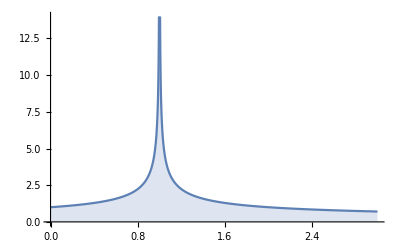

```mathematica
Plot[1/(((x-1)^2)^(1/4)),{x,0,3},PlotRange->{0,14},Filling->Axis]
```

불연속점에 대한 정보를 주더라도, NIntegrate가 계산하지 못할 수도 있습니다. 적분값이 실수로 한정되지 않는 경우입니다.

```mathematica
NIntegrate[1/((x-1)(x-2)),{x,0,1,2,3}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.9999999999999999999999999999836927356625087542212549245583116922}. NIntegrate obtained -146.633 and 28.7655 for the integral and error estimates.

-146.633